```mathematica
(*81 lines per section*)
(*r Zr-Zr C-Zr C-C Total*)
What are the objective of being able to classify Frenkel pairs?
```

What are the objective of being able to Classify Frenkels?
1) It is hugely time consuming to analyze defect-type in MD trajectories
2) Kinetics: we can estimate the type-lifetimes at different temperatures, and use this as means to estimate diffusion barriers
3) Thermodynamics: probe anharmonicity by comparing relative defect populations at TC to quasi-harmonic defect populations. It

## Classifier for Frenkel pairs

```mathematica
Ideas to improve the classifier:
1) Each volume has its own classifier
2) Difference the PDF with respect to an average perfect run at that temperature
3) Include Zr-C as well as C-C PDF
4) Include a few steps a high tempertures in the training model
```

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/"];
filesTrain={"pdf_OUT_129.4850/pdf.129.4850.300.1_1141.txt","pdf_OUT_142.4850/pdf.142.4850.300.1_891.txt",
"pdf_OUT_70.4850/m.pdf.70.4850.300.1_842.txt","pdf_OUT_174.4850/pdf.174.4850.300.1_851.txt",
"pdf_OUT_1126.4850/pdf.1126.4850.300.1_746.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.300.1_1071.txt"};


(*files={"pdf.70.4850.1_836.txt","pdf.129.4850.1_1141.txt","pdf.142.4850.1_891.txt","pdf.174.4850.1_851.txt","pdf.1126.4850.1_746.txt","pdf.PERF.4850.1_1071.txt"};*)
pdfData=Table[ReadList[filesTrain[[i]],{Number,Number,Number,Number,Number}],{i,1,6}];

names={"129","142","70","174","1126","PERF"};
temperatures={"300","760","1900","2500","3200","3805"};
fullNames={"Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-trimer","Unbound-tetramer","Perfect"};
header={"Methods","Bound-dimer","Bound-trimer","Unbound-dimer","Unbound-Trimer","Unbound-Tetramer","Perfect"};
(*volumes={"V=V(0.75T_C)","V=V(0.9T_C)"};*)

zrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[2]]},{i,1,6}];
czr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[3]]},{i,1,6}];
cc=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]]},{i,1,6}];
tot=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[5]]},{i,1,6}];
all=Table[Transpose@{Transpose[pdfData[[i]]][[2]],Transpose[pdfData[[i]]][[3]],Transpose[pdfData[[i]]][[4]]},{i,1,6}];
ccczr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]],Transpose[pdfData[[i]]][[3]]},{i,1,6}];
ccczrzrzr=Table[Transpose@{Transpose[pdfData[[i]]][[1]],Transpose[pdfData[[i]]][[4]],Transpose[pdfData[[i]]][[3]],Transpose[pdfData[[i]]][[2]]},{i,1,6}];

methods={"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"}
methodsProduction={"LogisticRegression","SupportVectorMachine"}

plotStyleA={PlotRange->All,PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r, t)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
```

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,RandomForest,SupportVectorMachine}

{LogisticRegression,SupportVectorMachine}

```mathematica
Table[zrzr[[i]]//Length,{i,1,Length@zrzr}]
```

{18549,14499,13689,13851,12150,17415}

### PDF plots

```mathematica
ListLinePlot[Partition[zrzr[[1]],81],PlotRange->All];
ListLinePlot[Partition[zrzr[[6]],81],PlotRange->All];
```

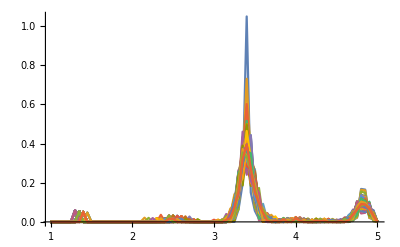
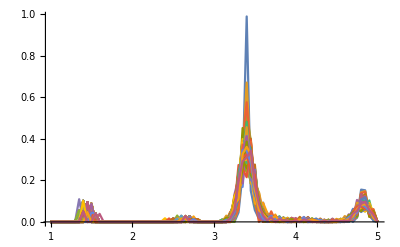
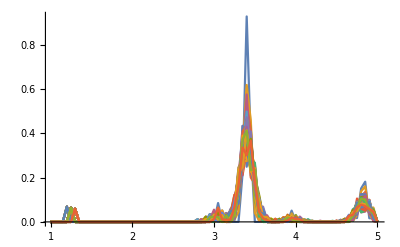
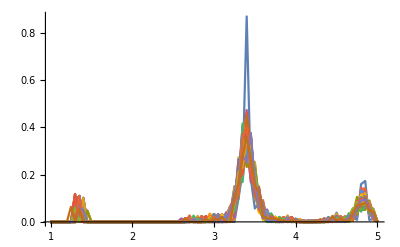
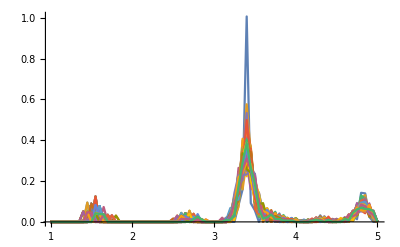

```mathematica
Table[ListLinePlot[Partition[cc[[i]],81],PlotRange->All],{i,1,5}]
```

```mathematica
ListLinePlot[Partition[tot[[1]],81][[1;;10]],PlotRange->All];
```

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name[[1]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[1]],81]//Length}],15]];
```

### PDF animations

```mathematica
ccAnimation=Table[With[{name=cc},ListAnimate[Table[ListLinePlot[Partition[name[[j]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,PlotLabel->fullNames[[j]],FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[j]],81]//Length}],25]],{j,1,6}];
```

$Aborted

```mathematica
(*Export["B2-test-data-300K.avi",ccAnimation[[1]],"Animation","AnimationRepetitions"->2,"ControlAppearance"->None]*)
plotStyle={PlotRange->{{0,5},{0,.5}},PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/animations"];
framesTrainingCC=Table[With[{name=cc},Table[ListLinePlot[Partition[name[[j]],81][[i]],plotStyle,PlotLabel->Style[fullNames[[j]],18,Black]],{i,1,Partition[name[[j]],81]//Length}]],{j,1,6}];
framesTrainingCCJoined=Join[framesTrainingCC[[1]],framesTrainingCC[[2]]];
(*Export["framesTrainingCC.gif",framesTrainingCCJoined,"AnimationRepetitions"->1,"ControlAppearance"->None,"FrameRate"->25]*)
```

```mathematica
With[{name=zrzr},ListAnimate[Table[ListLinePlot[Partition[name,81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name,81]//Length}],15]]
```

ListAnimate[{},15]

```mathematica
With[{name=czr},ListAnimate[Table[ListLinePlot[Partition[name[[1]],81][[i]],PlotRange->{{0,5},{0,.5}},Frame->True,FrameLabel->{"r (Å)","ρ(r)"}],{i,1,Partition[name[[1]],81]//Length}],15]]
```

## Train classifier

```mathematica
Table[Length[cc[[i]]]/81//N,{i,1,Length@cc}]
```

{229.,179.,169.,171.,150.,215.}

```mathematica
Options@Classify
methods={"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","RandomForest","SupportVectorMachine"}
```

{Method→Automatic,PerformanceGoal→Automatic,NominalVariables→Automatic,ValidationSet→None,FeatureNames→Automatic,FeatureTypes→Automatic,IndeterminateThreshold→Automatic,UtilityFunction→Automatic,Weights→Automatic,FeatureWeights→Automatic,DistributionPostProcessing→Automatic,PredictionName→Automatic,RecordLog→True,FeatureExtractor→None,ImputeMissingValues→True,ProcessorCaching→True,BatchProcessing→Automatic,MinimalPreprocessing→False,ClassPriors→Automatic,TieBreakerFunction→RandomChoice}

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,RandomForest,SupportVectorMachine}

### Standard

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsStandard=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.941176 | 1. | 1. | 0.921569 | 1.
0.647059 | 0.686275 | 0.803922 | 0.686275 | 0.705882 | 0.784314
0.941176 | 0.941176 | 1. | 1. | 0.901961 | 1.
0.529412 | 0.921569 | 0.980392 | 1. | 0.921569 | 1.
0.941176 | 0.941176 | 1. | 1. | 0.823529 | 1.
1. | 0.960784 | 1. | 1. | 0.980392 | 1.

```mathematica
(*trainingSet=50,ValidationSet=100*)
finalResultsStandard//TableForm
```

Methods | Bound-dimer | Bound-trimer | Unbound-dimer | Unbound-Trimer | Unbound-Tetramer | 
LogisticRegression | 0.941176 | 0.941176 | 1. | 1. | 0.921569 | 1.
Markov | 0.647059 | 0.686275 | 0.803922 | 0.686275 | 0.705882 | 0.784314
NaiveBayes | 0.941176 | 0.941176 | 1. | 1. | 0.901961 | 1.
NearestNeighbors | 0.529412 | 0.921569 | 0.980392 | 1. | 0.921569 | 1.
RandomForest | 0.941176 | 0.941176 | 1. | 1. | 0.823529 | 1.
SupportVectorMachine | 1. | 0.960784 | 1. | 1. | 0.980392 | 1.

### Explicit r index for c-c

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cc[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cc[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsExpl=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.941176 | 1. | 1. | 0.921569 | 1.
0.666667 | 0.666667 | 0.803922 | 0.666667 | 0.705882 | 0.686275
0.941176 | 0.941176 | 1. | 1. | 0.901961 | 1.
0.529412 | 0.921569 | 0.980392 | 1. | 0.921569 | 1.
0.980392 | 0.941176 | 1. | 1. | 1. | 1.
1. | 0.960784 | 1. | 1. | 0.980392 | 1.

### Log

```mathematica
{#[[1]],2#[[2]]}&/@Transpose@{{1,2,3,4},{10,11,12,13}};
funny={#[[1]],#[[2]]-#[[3]]}&;
funny/@Transpose@{{1,2,3,4},{10,11,12,13},{10,11,12,23}};
```

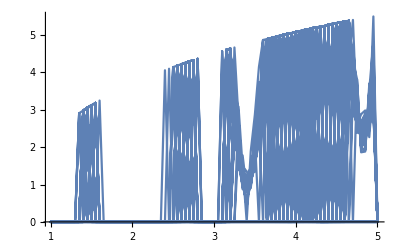

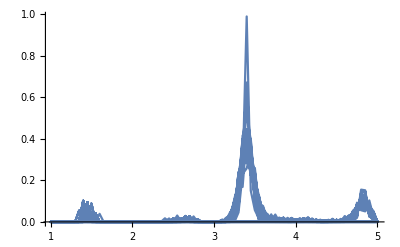

```mathematica
loggy={#[[1]],-Log@#[[2]]/.Indeterminate->0}&;
ListLinePlot[loggy/@cc[[2]][[1;;5000]],PlotRange->All]
ListLinePlot[cc[[2]][[1;;5000]],PlotRange->All]
```

```mathematica
cclog=Table[loggy/@cc[[type]],{type,1,6}];
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[cclog[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[cclog[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsLog=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.901961 | 0.941176 | 1. | 1. | 0.843137 | 1.
0.588235 | 0.54902 | 0.862745 | 0.666667 | 0.745098 | 0.764706
0.980392 | 0.921569 | 1. | 1. | 0.882353 | 1.
0.588235 | 0.921569 | 1. | 1. | 0.901961 | 1.
0.941176 | 0.901961 | 1. | 0.980392 | 0.764706 | 1.
0.960784 | 0.960784 | 1. | 1. | 0.882353 | 1.

### Joint space c-c and c-zr

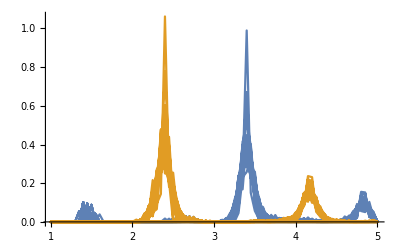

```mathematica
ListLinePlot[{cc[[2]][[1;;5000]],czr[[2]][[1;;5000]]},PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccczr[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccczr[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsJoint=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

1. | 0.921569 | 1. | 1. | 0.921569 | 1.
0.607843 | 0.627451 | 0.705882 | 0.666667 | 0.72549 | 0.980392
0.843137 | 0.980392 | 1. | 1. | 0.941176 | 1.
0.647059 | 0.941176 | 1. | 1. | 0.921569 | 1.
0.921569 | 0.960784 | 1. | 0.980392 | 0.901961 | 1.
1. | 0.960784 | 1. | 1. | 1. | 1.

### Three part joint space - c-c c-zr zr-zr

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccczrzrzr[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccczrzrzr[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsJoint3=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.882353 | 1. | 1. | 0.882353 | 1.
0.627451 | 0.529412 | 0.705882 | 0.745098 | 0.686275 | 0.960784
0.882353 | 0.980392 | 1. | 1. | 0.941176 | 1.
0.764706 | 0.921569 | 1. | 1. | 0.862745 | 1.
0.901961 | 0.980392 | 1. | 1. | 0.803922 | 1.
0.980392 | 0.941176 | 1. | 1. | 0.921569 | 1.

### Sum space for c-c plus c-zr

```mathematica
ccsum;
```

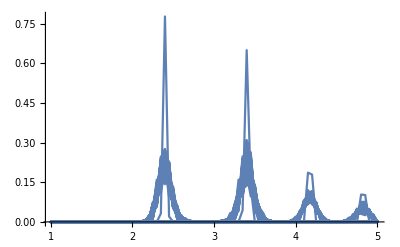

```mathematica
summy={#[[1]],0.5*(#[[2]]+#[[3]])}&;
ccsum=Table[summy/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccsum[[6]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsum[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsum[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.980392 | 0.921569 | 1. | 1. | 0.941176 | 1.
0.627451 | 0.431373 | 0.843137 | 0.568627 | 0.607843 | 0.882353
0.843137 | 0.823529 | 0.960784 | 1. | 0.980392 | 1.
0.960784 | 0.941176 | 1. | 0.980392 | 0.921569 | 1.
0.901961 | 0.941176 | 1. | 1. | 0.980392 | 1.
0.980392 | 0.980392 | 1. | 1. | 1. | 1.

### Sum space for c-c and zr-c, and for c-c and zr-zr

```mathematica
summy4={#[[1]],0.5*(#[[2]]+#[[3]]),0.5*(#[[2]]+#[[4]])}&;
ccsum4=Table[summy4/@ccczrzrzr[[type]],{type,1,6}];
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsum4[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsum4[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum4=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.980392 | 0.960784 | 1. | 1. | 0.901961 | 1.
0.627451 | 0.647059 | 0.843137 | 0.686275 | 0.745098 | 0.980392
0.862745 | 0.960784 | 1. | 1. | 1. | 1.
0.941176 | 0.980392 | 1. | 1. | 0.882353 | 1.
0.980392 | 0.960784 | 1. | 1. | 0.901961 | 1.
0.980392 | 0.980392 | 1. | 1. | 0.980392 | 1.

### Sum space for c-c plus c-zr

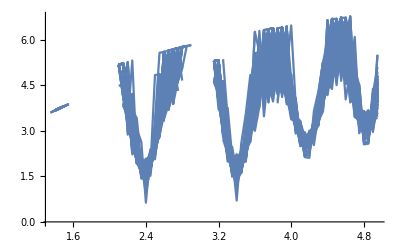

```mathematica
summyL={#[[1]],-Log[0.5*(#[[2]]+#[[3]])]}&;
ccsumL=Table[summyL/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccsumL[[2]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsumL[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsumL[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.235294 | 0.333333 | 0.607843 | 0.784314 | 0.862745 | 0.941176
0.431373 | 0.294118 | 0.509804 | 0.529412 | 0.313725 | 0.882353
0.745098 | 0.666667 | 0.901961 | 0.941176 | 0.901961 | 0.960784
0.137255 | 0.313725 | 0.45098 | 0.588235 | 0.784314 | 0.960784
0.254902 | 0.54902 | 0.509804 | 0.764706 | 0.764706 | 0.921569
0.45098 | 0.568627 | 0.784314 | 0.882353 | 0.823529 | 0.941176

```mathematica
Sum space for c-c plus zr-zr
```

-zr+for space Sum ClassifierFunction[…]-plus zr ClassifierFunction[…]

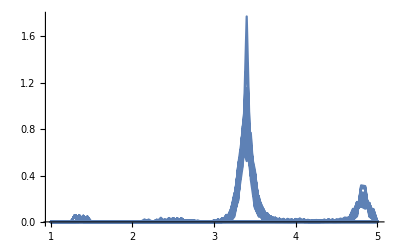

```mathematica
summy2={#[[1]],(#[[2]]+#[[4]])}&;
ccsum2=Table[summy2/@ccczrzrzr[[type]],{type,1,6}];
ListLinePlot[ccsum2[[1]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsum2[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsum2[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum2=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.980392 | 0.980392 | 1. | 1. | 0.921569 | 1.
0.509804 | 0.705882 | 0.784314 | 0.882353 | 0.666667 | 0.882353
0.803922 | 0.960784 | 1. | 1. | 0.980392 | 1.
0.941176 | 0.960784 | 1. | 1. | 0.882353 | 1.
0.921569 | 0.921569 | 1. | 1. | 0.941176 | 1.
0.980392 | 0.980392 | 1. | 1. | 0.980392 | 1.

### Sum space for c-c plus zr-zr plus zr-c

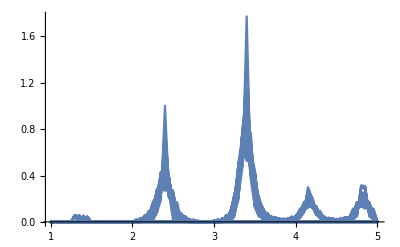

```mathematica
summy3={#[[1]],(#[[2]]+#[[3]]+#[[4]])}&;
ccsum3=Table[summy3/@ccczrzrzr[[type]],{type,1,6}];
ListLinePlot[ccsum3[[1]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccsum3[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccsum3[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsSum3=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.921569 | 1. | 1. | 0.941176 | 1.
0.607843 | 0.54902 | 0.686275 | 0.627451 | 0.607843 | 0.921569
0.784314 | 0.823529 | 0.980392 | 0.980392 | 1. | 1.
0.980392 | 0.921569 | 0.980392 | 1. | 0.901961 | 1.
1. | 0.941176 | 1. | 0.980392 | 0.941176 | 1.
0.980392 | 0.960784 | 1. | 1. | 1. | 1.

### Diff c-c minus zr-zr

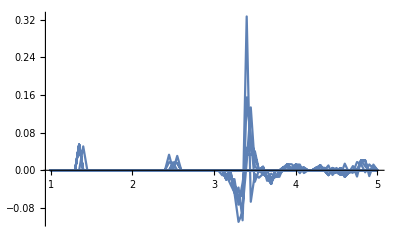

```mathematica
diff2={#[[1]],(#[[2]]-#[[4]])}&;
ccdiff2=Table[diff2/@ccczrzrzr[[type]],{type,1,6}];
ListLinePlot[ccdiff2[[1]][[1;;400]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiff2[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiff2[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiff2=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.862745 | 0.960784 | 1. | 0.980392 | 0.941176 | 1.
0.568627 | 0.666667 | 0.921569 | 0.745098 | 0.705882 | 1.
0.784314 | 0.901961 | 0.960784 | 1. | 0.823529 | 1.
0.45098 | 0.843137 | 1. | 0.882353 | 0.705882 | 1.
0.941176 | 0.980392 | 0.980392 | 1. | 0.921569 | 0.980392
0.901961 | 0.960784 | 1. | 1. | 0.960784 | 1.

### Diff c-c minus c-zr abs

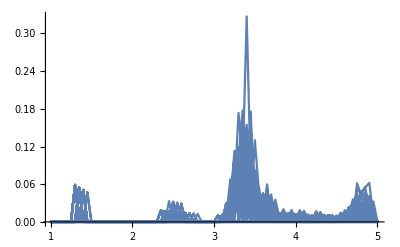

```mathematica
diff3={#[[1]],Abs@(#[[2]]-#[[4]])}&;
ccdiff3=Table[diff3/@ccczrzrzr[[type]],{type,1,6}];
ListLinePlot[ccdiff3[[1]][[1;;4000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiff3[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiff3[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiff3=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.784314 | 0.921569 | 1. | 1. | 0.960784 | 1.
0.470588 | 0.54902 | 0.745098 | 0.647059 | 0.666667 | 0.823529
0.803922 | 0.882353 | 1. | 1. | 0.823529 | 1.
0.352941 | 0.843137 | 0.980392 | 0.882353 | 0.764706 | 1.
0.941176 | 0.882353 | 0.980392 | 1. | 0.960784 | 1.
0.843137 | 0.941176 | 0.960784 | 1. | 0.960784 | 1.

### Diff c-c minus zr-zr and c-c plus zr-c

```mathematica
diffsum={#[[1]],(#[[2]]-#[[4]]),(#[[2]]+#[[3]])}&;
ccdiffsum=Table[diffsum/@ccczrzrzr[[type]],{type,1,6}];
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiffsum[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiffsum[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiffSum=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

$Aborted

### Diff space for c-c minus c-zr

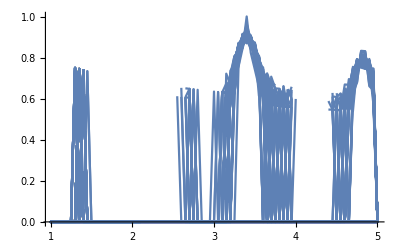

```mathematica
diffy={#[[1]],(#[[2]]-#[[3]])^0.1}&;
ccdiff=Table[diffy/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccdiff[[1]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiff[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiff[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiff=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.882353 | 0.882353 | 1. | 0.941176 | 0.823529 | 1.
0.647059 | 0.529412 | 0.745098 | 0.607843 | 0.705882 | 0.901961
0.705882 | 0.882353 | 0.921569 | 0.980392 | 0.803922 | 1.
0.843137 | 0.921569 | 0.921569 | 0.764706 | 0.784314 | 1.
0.882353 | 0.960784 | 1. | 0.980392 | 0.784314 | 1.
0.921569 | 0.901961 | 1. | 0.941176 | 0.784314 | 1.

### Difference c-c minus zr-zr with absolute

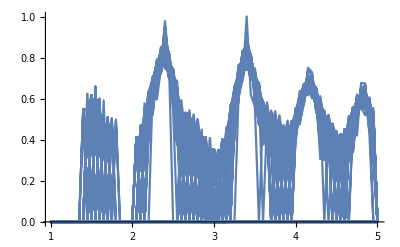

```mathematica
diffyAbs={#[[1]],((#[[2]]-#[[3]])^2)^0.1}&;
ccdiffAbs=Table[diffyAbs/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccdiffAbs[[5]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiffAbs[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiffAbs[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiff=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.921569 | 0.901961 | 0.980392 | 0.901961 | 0.862745 | 1.
0.72549 | 0.647059 | 0.764706 | 0.568627 | 0.588235 | 0.901961
0.784314 | 0.843137 | 0.960784 | 1. | 0.803922 | 1.
0.960784 | 0.921569 | 0.960784 | 0.921569 | 0.901961 | 1.
0.901961 | 0.921569 | 1. | 0.980392 | 0.745098 | 1.
0.921569 | 0.960784 | 0.980392 | 0.921569 | 0.882353 | 1.

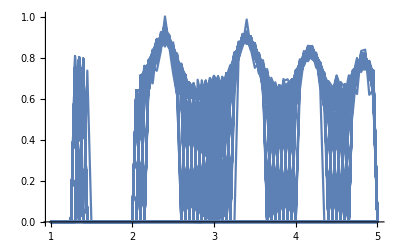

```mathematica
diffyAbs2={#[[1]],Abs[(#[[2]]-#[[3]])]^0.1}&;
ccdiffAbs2=Table[diffyAbs2/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccdiffAbs2[[4]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiffAbs2[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiffAbs2[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiffAbs2=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.882353 | 0.882353 | 0.980392 | 0.901961 | 0.862745 | 1.
0.705882 | 0.588235 | 0.823529 | 0.529412 | 0.588235 | 0.901961
0.784314 | 0.843137 | 0.960784 | 1. | 0.784314 | 1.
0.941176 | 0.941176 | 0.941176 | 0.921569 | 0.843137 | 1.
0.941176 | 0.921569 | 1. | 0.941176 | 0.784314 | 1.
0.901961 | 0.960784 | 0.980392 | 0.921569 | 0.862745 | 1.

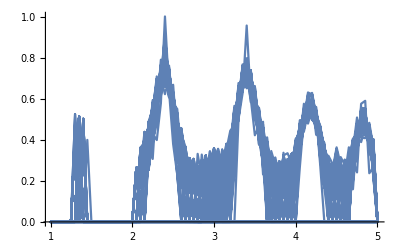

```mathematica
diffyAbs3={#[[1]],Abs[(#[[2]]-#[[3]])]^0.3}&;
ccdiffAbs3=Table[diffyAbs3/@ccczr[[type]],{type,1,6}];
ListLinePlot[ccdiffAbs3[[4]][[1;;10000]],PlotRange->All]
```

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[ccdiffAbs3[[type]],81][[timeStep]]][[2]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[ccdiffAbs3[[type]],81][[timeStep]]][[2]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsDiffAbs2=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.941176 | 0.882353 | 0.980392 | 0.901961 | 0.862745 | 1.
0.745098 | 0.607843 | 0.823529 | 0.509804 | 0.588235 | 0.901961
0.784314 | 0.843137 | 0.960784 | 1. | 0.803922 | 1.
0.960784 | 0.843137 | 0.980392 | 0.921569 | 0.862745 | 1.
0.901961 | 0.921569 | 1. | 0.941176 | 0.72549 | 1.
0.901961 | 0.960784 | 0.980392 | 0.921569 | 0.901961 | 1.

### All

```mathematica
scores=With[{maxTypes=6},Table[results=With[{trainSize=50,valSize=50,method=methods[[i]]},trainSet=Join@@Table[Table[Transpose[Partition[all[[type]],81][[timeStep]]]->ToString@fullNames[[type]],{timeStep,1,trainSize}],{type,1,maxTypes}];
c=Classify[trainSet,Method->method,PerformanceGoal->"Quality"];
Table[Table[c[Transpose[Partition[all[[type]],81][[timeStep]]]],{type,1,maxTypes}],{timeStep,trainSize,trainSize+valSize}]];
(*results for 10 training eras*)
accuracy=Table[{fullNames[[type]],Count[Transpose[results][[type]],Transpose[results][[type]][[1]]]/Length[Transpose[results][[type]]]//N},{type,1,maxTypes}];
Transpose[accuracy][[2]],{i,1,6}]//TableForm]
finalResultsAll=With[{maxTypes=6},Join[{header[[1;;maxTypes]]},Table[Flatten@Join[{methods[[i]],scores[[1]][[i]]}],{i,1,Length@methods}]]];
```

0.960784 | 0.882353 | 1. | 1. | 0.901961 | 1.
0.647059 | 0.509804 | 0.72549 | 0.764706 | 0.666667 | 0.980392
0.882353 | 0.980392 | 1. | 1. | 0.941176 | 1.
0.843137 | 0.921569 | 1. | 1. | 0.921569 | 1.
0.980392 | 0.941176 | 1. | 0.980392 | 0.941176 | 1.
0.980392 | 0.941176 | 1. | 1. | 0.921569 | 1.

#### Conclusions

The support vector Machine, and linear logistic regression kernel are both pretty tight. The best results are obtained for c-c + zr-c, so lets use that therefore to train a production linear and support vector vector

```mathematica
plotStyleA={PlotRange->All,PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["r (Å)",18,Black],Style["ρ(r, t)",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
```

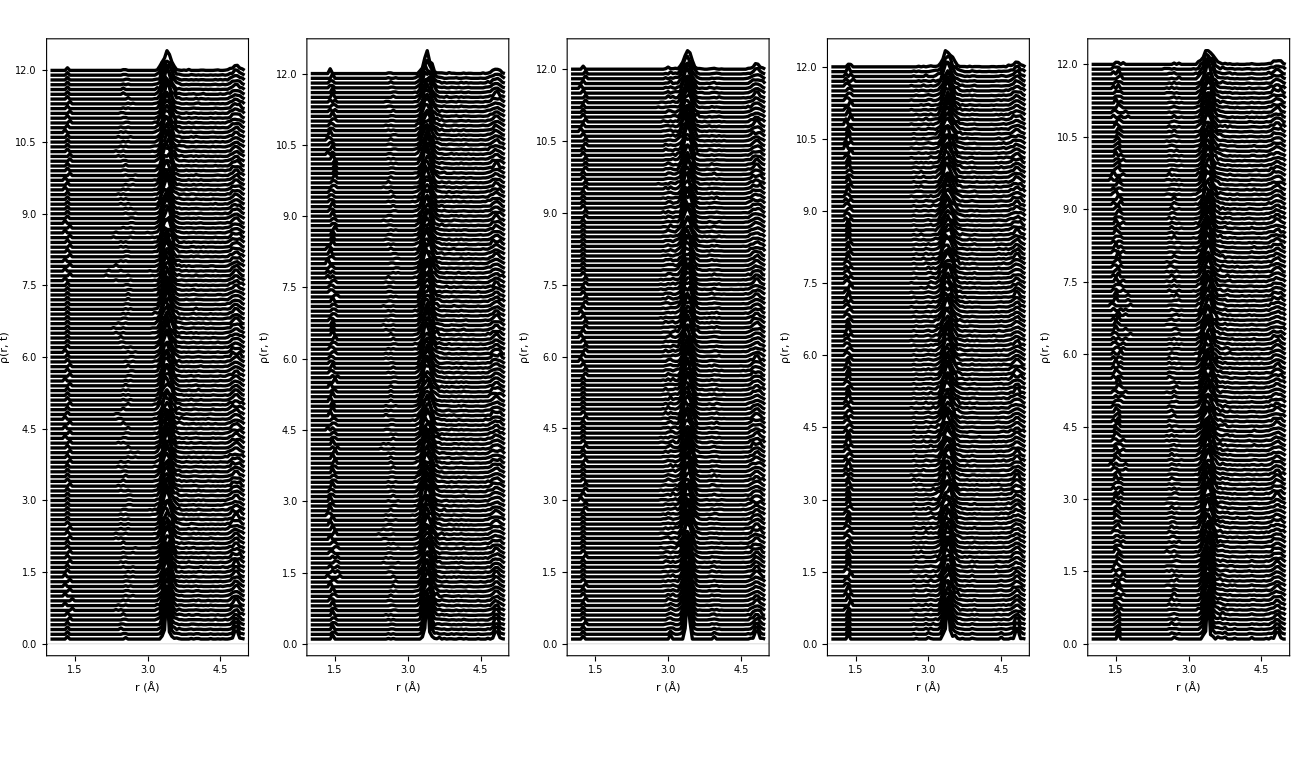

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[cc[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,120}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

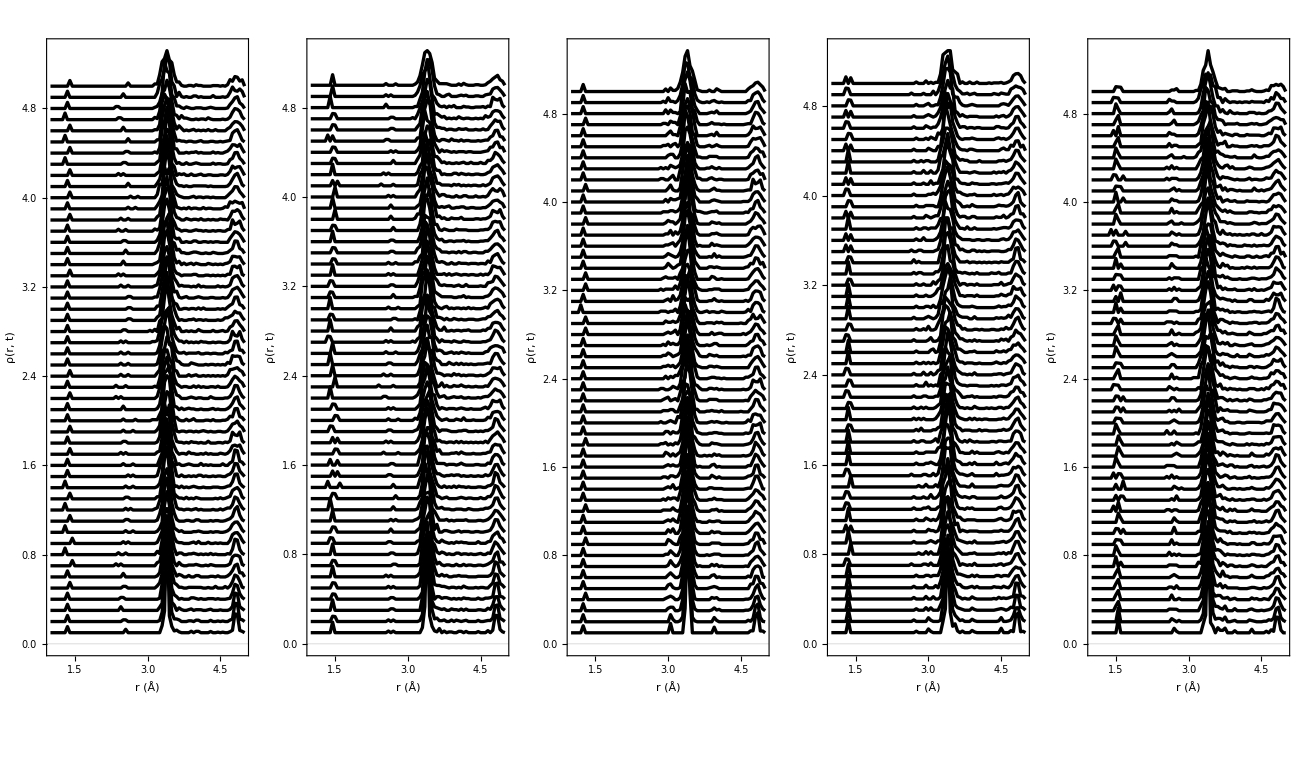

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[cc[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,50}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

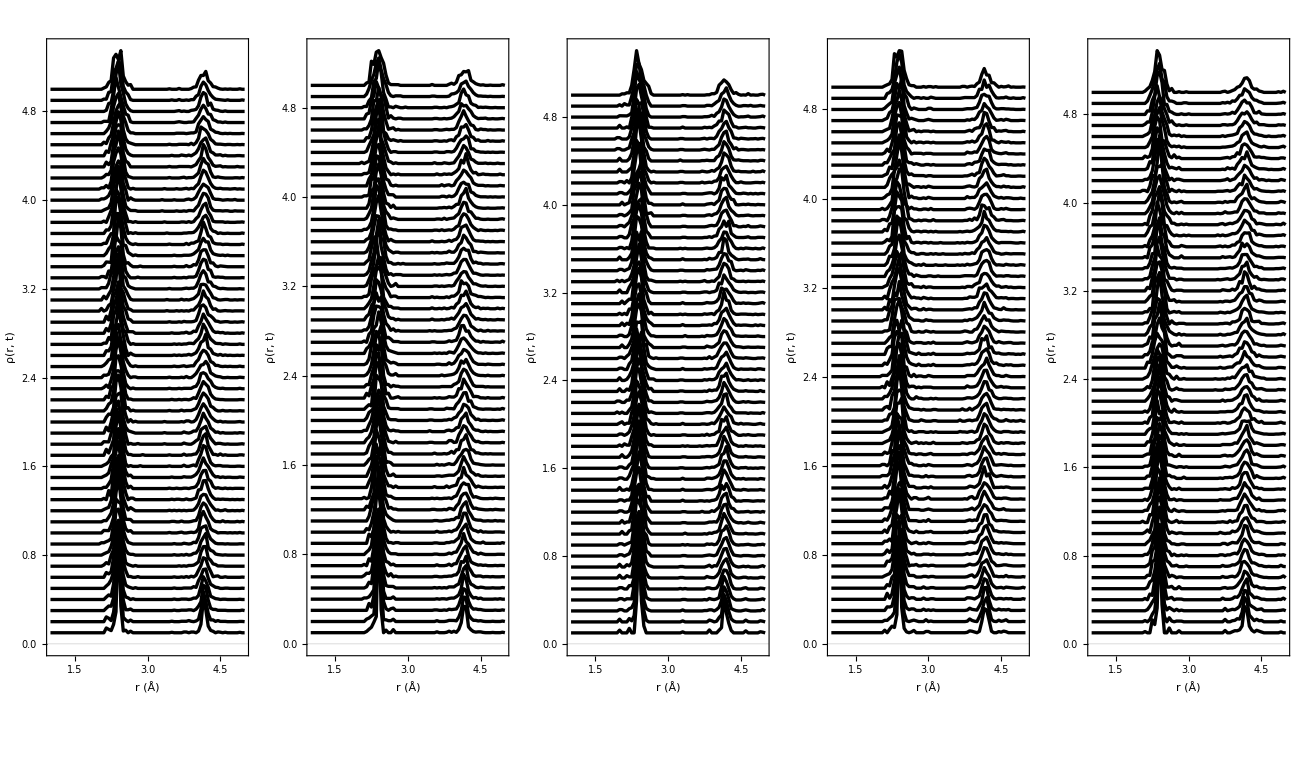

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[czr[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,50}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

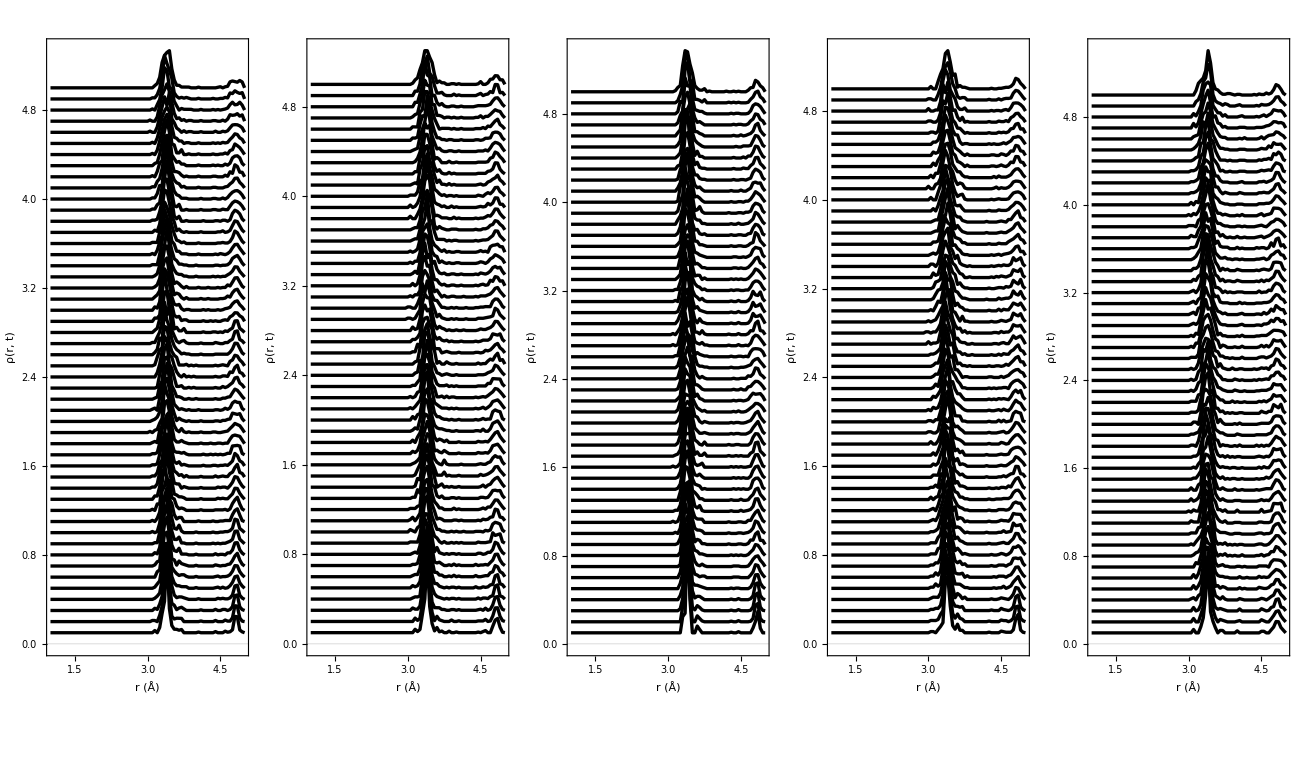

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[zrzr[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,50}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

## Production machine

Steps:
1) Import data at each temperature for each defect. 
2) Train a linear and SVMs on Initial 300K + 760K.
3) Train a bigger model on all temperatures

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results"];
(*Perfect*)
filesTestPerf={"pdf_OUT_perf.4850/m.pdf.PERF.4850.300.1_1071.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.760.1_186.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.1900.1_191.txt",
"pdf_OUT_perf.4850/m.pdf.PERF.4850.2500.1_166.txt","pdf_OUT_perf.4850/m.pdf.PERF.4850.3200.1_156.txt",
"pdf_OUT_perf.4850/m.pdf.PERF.4850.3805.1_151.txt"};
(*Bound*)
filesTest129={"pdf_OUT_129.4850/pdf.129.4850.300.1_1141.txt","pdf_OUT_129.4850/normal/m.pdf.129.4850.760.B2-01_129.txt","pdf_OUT_129.4850/normal/m.pdf.129.4850.1900.B2-01_108.txt",
"pdf_OUT_129.4850/normal/m.pdf.129.4850.2500.B2-01_45.txt","pdf_OUT_129.4850/normal/m.pdf.129.4850.3200.B2-01_30.txt",
"pdf_OUT_129.4850/normal/m.pdf.129.4850.3805.B2-01_28.txt"};
filesTest142={"pdf_OUT_142.4850/pdf.142.4850.300.1_891.txt","pdf_OUT_142.4850/normal/m.pdf.142.4850.760.B3-01_217.txt","pdf_OUT_142.4850/normal/m.pdf.142.4850.1900.B3-01_111.txt",
"pdf_OUT_142.4850/normal/m.pdf.142.4850.2500.B3-01_109.txt","pdf_OUT_142.4850/normal/m.pdf.142.4850.3200.B3-01_60.txt",
"pdf_OUT_142.4850/normal/m.pdf.142.4850.3805.B3-01_20.txt"};
(*Unbound*)
filesTest70={"pdf_OUT_70.4850/m.pdf.70.4850.300.1_842.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.760.U2-01_223.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.1900.U2-01_169.txt",
"pdf_OUT_70.4850/normal/m.pdf.70.4850.2500.U2-01_171.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.3200.U2-01_169.txt",
"pdf_OUT_70.4850/normal/m.pdf.70.4850.3805.U2-01_121.txt"};
filesTest174={"pdf_OUT_174.4850/pdf.174.4850.300.1_851.txt","pdf_OUT_174.4850/normal/m.pdf.174.4850.760.U3-01_171.txt","pdf_OUT_174.4850/normal/m.pdf.174.4850.1900.U3-01_197.txt",
"pdf_OUT_174.4850/normal/m.pdf.174.4850.2500.U3-01_166.txt","pdf_OUT_174.4850/normal/m.pdf.174.4850.3200.U3-01_81.txt",
"pdf_OUT_174.4850/normal/m.pdf.174.4850.3805.U3-01_158.txt"};

filesTest1126={"pdf_OUT_1126.4850/pdf.1126.4850.300.1_746.txt","pdf_OUT_1126.4850/normal/m.pdf.1126.4850.760.U4-01_176.txt","pdf_OUT_1126.4850/normal/m.pdf.1126.4850.1900.U4-01_69.txt",
"pdf_OUT_1126.4850/normal/m.pdf.1126.4850.2500.U4-01_67.txt","pdf_OUT_1126.4850/normal/m.pdf.1126.4850.3200.U4-01_54.txt",
"pdf_OUT_1126.4850/normal/m.pdf.1126.4850.760.U4-01_176.txt"};
filesDefectTypes={filesTest129,filesTest142,filesTest70,filesTest174,filesTest1126,filesTestPerf};
pdfDataProTest=Table[Table[ReadList[filesDefectTypes[[type]][[temp]],{Number,Number,Number,Number,Number}],{temp,1,Length@filesDefectTypes[[type]]}],{type,1,6}];
proSum={#[[1]],0.5*(#[[3]]+#[[4]])}&;
proSum2={#[[1]],#[[4]]}&;
(*pdfDataProTest=Table[Table[ReadList[files[[j]][[i]],{Number,Number,Number,Number,Number}],{i,1,Length@files[[j]]}],{j,1,Length@files}]*)
```

```mathematica
pdfDataProTest[[defectType_]][[temperature_]]
```

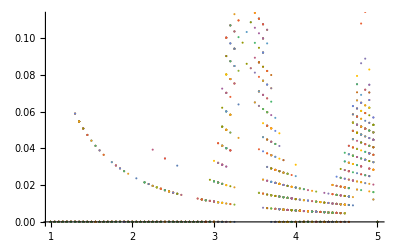

```mathematica
ListPlot@Table[Table[proSum2/@Partition[pdfDataProTest[[1]][[j]],81][[i]],{i,1,Length@Partition[pdfDataProTest[[1]][[j]],81]}],{j,1,Length@pdfDataProTest[[1]]}][[4]]
```

### Bound Dimer

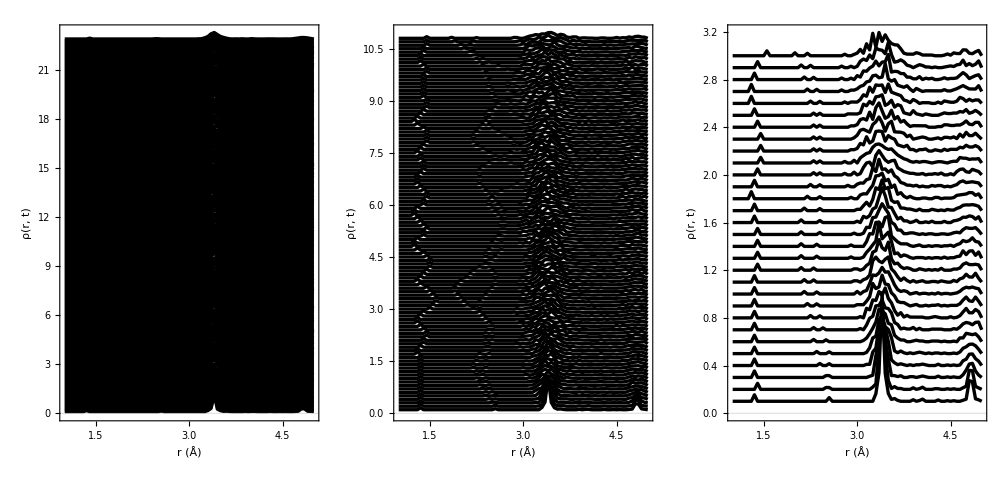

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum2/@Partition[pdfDataProTest[[1]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[1]][[j]],81]}],plotStyleA,AspectRatio->1.5],{j,1,6,2}]},ImageSize->1000,Spacings->2]
```

### Bound trimer

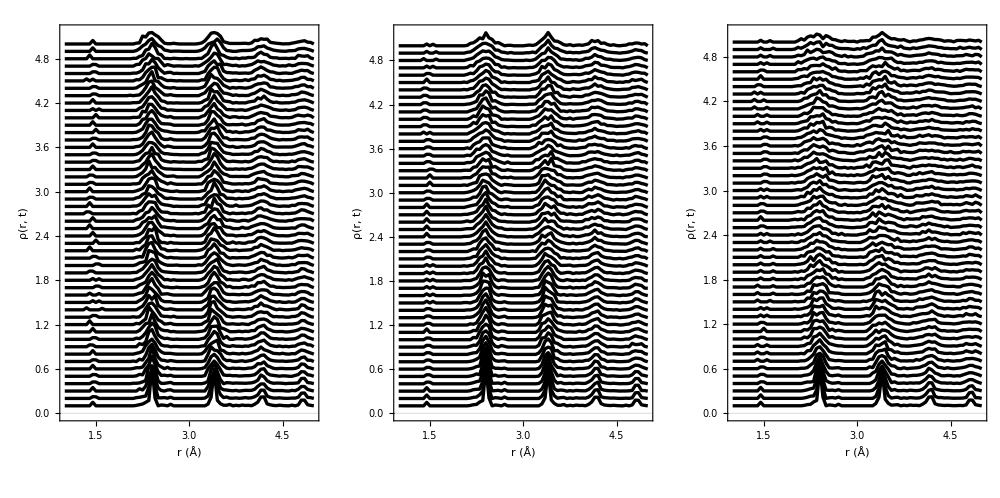

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[2]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[2]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,3}]},ImageSize->1000,Spacings->2]
```

### Unbound dimer

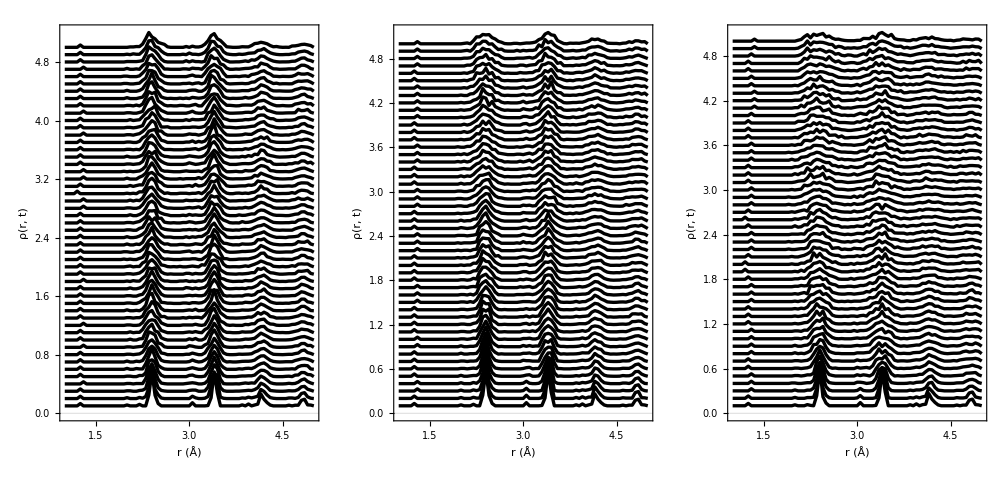

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[3]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[3]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,3}]},ImageSize->1000,Spacings->2]
```

### Unbound trimer

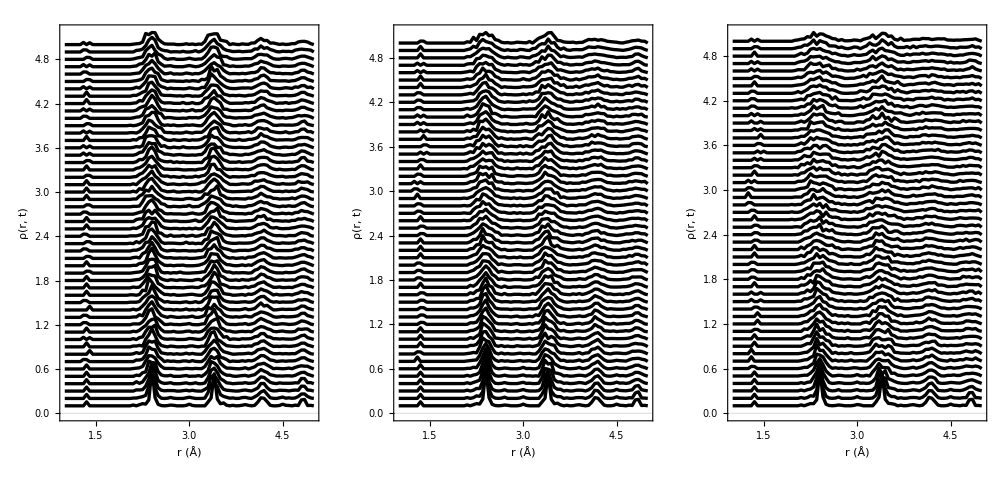

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[4]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[4]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,3}]},ImageSize->1000,Spacings->2]
```

### Unbound tetramer

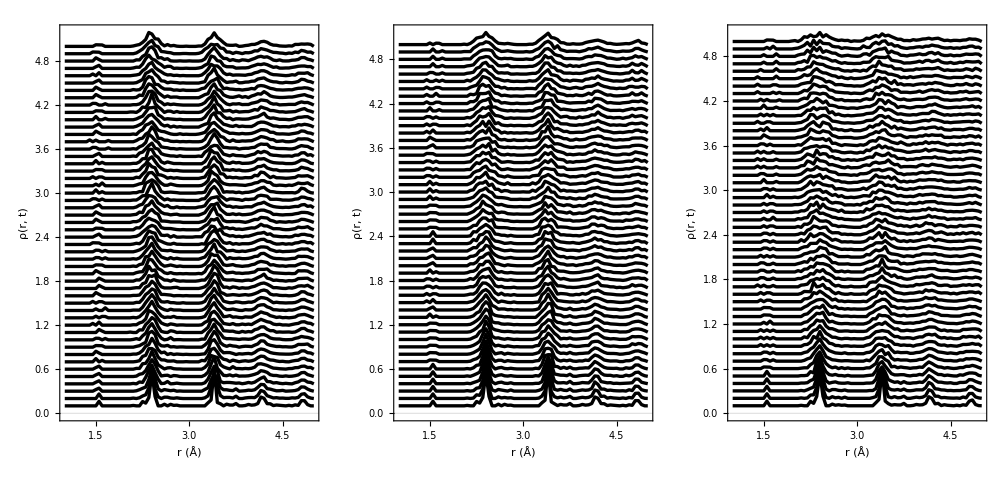

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[proSum/@Partition[pdfDataProTest[[5]][[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,Length@Partition[pdfDataProTest[[5]][[j]],81]}][[1;;50]],plotStyleA,AspectRatio->1.5],{j,1,3}]},ImageSize->1000,Spacings->2]
```

### 2-temperatures, 5-defects training

```mathematica
(*Model training*)
cSVM=With[{maxTypes=5,maxTemps=1,method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum2/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTemps}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
]
```

$Aborted

### 5-temps, 5 defects testing

```mathematica
(*Model testing*)
With[{maxTypes=5,maxTemps=5,method=methodsProduction[[2]],maxTempsTrain=1},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTemps}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTemps}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTemps}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTemps}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temps: ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
```

Model type: SupportVectorMachine, with training temps: {300}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200
Bound-dimer | 1. | 0.379845 | 0.12963 | 0.177778 | 0.2
Bound-trimer | 1. | 0.21659 | 0.0810811 | 0.0642202 | 0.1
Unbound-dimer | 1. | 0.2287 | 0.0769231 | 0.0408163 | 0.035503
Unbound-trimer | 1. | 0.426901 | 0.0659898 | 0.0361446 | 0.0617284
Unbound-tetramer | 1. | 1. | 1. | 1. | 1.

## Robustness of SVM classifier to new non-training temperatures -- transferability

### T=300K trained classifier

```mathematica
Module[{maxTempsTrain=1,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum2/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum2/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 0.79845 | 0.231481 | 0.177778 | 0.4 | 0.357143
Bound-trimer | 1. | 0.410138 | 0.117117 | 0.0642202 | 0.1 | 0.3
Unbound-dimer | 1. | 0.569507 | 0.0887574 | 0.0408163 | 0.0414201 | 0.0413223
Unbound-trimer | 1. | 0.766082 | 0.0862944 | 0.0481928 | 0.0740741 | 0.0316456
Unbound-tetramer | 1. | 1. | 1. | 1. | 1. | 1.
Perfect | 1. | 0.184211 | 0.025641 | 0.0294118 | 0.03125 | 0.0322581

### T={300K, 760K} trained classifier

```mathematica
Module[{maxTempsTrain=2,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 0.25 | 0.4 | 0.533333 | 0.464286
Bound-trimer | 1. | 1. | 0.252252 | 0.155963 | 0.233333 | 0.55
Unbound-dimer | 1. | 1. | 0.295858 | 0.142857 | 0.118343 | 0.140496
Unbound-trimer | 1. | 1. | 0.340102 | 0.144578 | 0.222222 | 0.0886076
Unbound-tetramer | 1. | 1. | 1. | 1. | 1. | 1.
Perfect | 1. | 1. | 0.0512821 | 0.0294118 | 0.03125 | 0.0322581

### T={300K,760K,1900K} trained classifier

```mathematica
Module[{maxTempsTrain=3,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760, 1900}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 1. | 0.844444 | 1. | 0.892857
Bound-trimer | 1. | 1. | 1. | 0.715596 | 0.75 | 0.8
Unbound-dimer | 1. | 1. | 1. | 0.964286 | 0.751479 | 0.586777
Unbound-trimer | 1. | 1. | 1. | 0.909639 | 0.851852 | 0.746835
Unbound-tetramer | 1. | 1. | 1. | 0.955224 | 0.851852 | 1.
Perfect | 1. | 1. | 1. | 1. | 1. | 0.709677

### T={300K, 760K, 1900K, 2500K} trained classifier

```mathematica
Module[{maxTempsTrain=4,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760, 1900, 2500}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 1. | 1. | 1. | 0.857143
Bound-trimer | 1. | 1. | 1. | 1. | 0.783333 | 0.9
Unbound-dimer | 1. | 1. | 1. | 1. | 0.940828 | 0.859504
Unbound-trimer | 1. | 1. | 1. | 1. | 0.91358 | 0.810127
Unbound-tetramer | 1. | 1. | 1. | 1. | 0.87037 | 1.
Perfect | 1. | 1. | 1. | 1. | 1. | 0.870968

### T={300K, 760K, 1900K, 2500K, 3200K} trained classifier

```mathematica
Module[{maxTempsTrain=5,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760, 1900, 2500, 3200}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 1. | 1. | 1. | 0.892857
Bound-trimer | 1. | 1. | 1. | 1. | 1. | 0.95
Unbound-dimer | 1. | 1. | 1. | 1. | 1. | 0.966942
Unbound-trimer | 1. | 1. | 1. | 1. | 1. | 0.71519
Unbound-tetramer | 1. | 1. | 1. | 1. | 1. | 1.
Perfect | 1. | 1. | 1. | 1. | 1. | 1.

### T={300K, 760K, 1900K, 2500K, 3200K, 3805K} trained classifier

```mathematica
methodsProduction[[2]]
```

SupportVectorMachine

```mathematica
Module[{maxTempsTrain=6,maxTempsTest=6,maxTypes=6},

cSVM=With[{method=methodsProduction[[2]]},
(*Define a training set*)
trainingSet=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]]->ToString@fullNames[[type]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTrain}],{type,1,maxTypes}];

(*Collapse the training set dimensions into one big set*)
twoTempsTrainingFlat=Join@@Join@@trainingSet;
(*Run the classifier*)
Classify[twoTempsTrainingFlat,Method->method,PerformanceGoal->"Quality"]
];

(*Model testing*)
With[{method=methodsProduction[[2]]},

(*Define the teseting or validation data set*)
valData=Table[Table[Table[proSum/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Apply the model to a test set*)
results=Table[Table[Table[cSVM[valData[[type]][[temp]][[timeStep]]],{timeStep,1,Length@valData[[type]][[temp]]}],{temp,1,maxTempsTest}],{type,1,maxTypes}];

(*Results presentation*)
accuracy=Table[Table[Count[results[[type]][[temp]],fullNames[[type]]]/Length[results[[type]][[temp]]]//N,{temp,1,maxTempsTest}],{type,1,maxTypes}];
tList=Table[temperatures[[temp]],{temp,1,maxTempsTest}];
typeList=Table[fullNames[[type]],{type,1,maxTypes}];
typeListTemps=Join@@{{"Temperatures:"},typeList};
message=StringJoin["Model type: ",ToString@method,", with training temperatures (K): ",ToString@tList[[1;;maxTempsTrain]]];
(*{message,Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}}//TableForm*)
{{message},Transpose[Join@@{{typeListTemps},Transpose@Join[{tList},accuracy]}]//TableForm}//TableForm
]
]
```

Model type: SupportVectorMachine, with training temperatures (K): {300, 760, 1900, 2500, 3200, 3805}
Temperatures: | 300 | 760 | 1900 | 2500 | 3200 | 3805
Bound-dimer | 1. | 1. | 1. | 1. | 1. | 1.
Bound-trimer | 1. | 1. | 1. | 1. | 1. | 1.
Unbound-dimer | 1. | 1. | 1. | 1. | 1. | 1.
Unbound-trimer | 1. | 1. | 1. | 1. | 1. | 1.
Unbound-tetramer | 1. | 1. | 1. | 1. | 1. | 1.
Perfect | 1. | 1. | 1. | 1. | 1. | 1.

```mathematica
cSVM
```

ClassifierFunction[…]

```mathematica
(*Doesn't work: Export["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet.C-C-allT-cSVM.wlnet",cSVM]*)
```

## Visualise the classification space

{6,6}

{229,81,2}

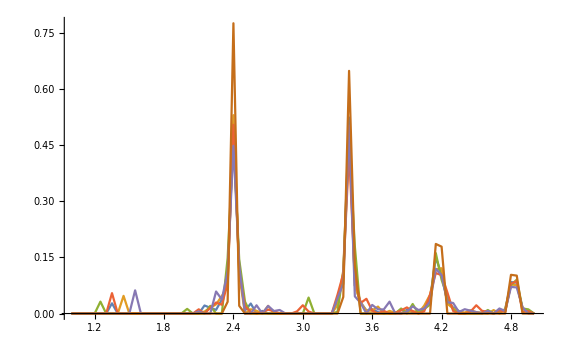

```mathematica
valData//Dimensions
valData[[1]][[1]]//Dimensions
typeExamples=Table[valData[[types]][[1]][[1]],{types,1,6}];
ListLinePlot[typeExamples,PlotRange->All]
```

```mathematica
Options@FeatureExtract
```

{PerformanceGoal→Automatic,NominalVariables→Automatic,FeatureNames→Automatic,FeatureTypes→Automatic,Weights→Automatic,FeatureWeights→Automatic,ProcessorCaching→False,OutputWrapper→Automatic,RecordLog→True}

```mathematica
feet=FeatureExtract[typeExamples]
xy=DimensionReduce[feet,2]
xyz=DimensionReduce[feet,3]
```

{{0.90131,-0.0408584,1.73969,-3.59014,3.85262},{2.00394,1.19871,0.115205,-4.53917,-3.33151},{-3.04614,-4.78463,-5.50597,0.227725,0.0946008},{1.89683,-4.49966,4.86153,2.98579,-0.83795},{6.04265,3.97145,-2.68995,3.30161,0.492337},{-7.79858,4.15499,1.47948,1.61418,-0.270092}}

{{-0.205802,0.0113773},{-0.457686,-0.33344},{0.696031,1.32973},{-0.433012,1.25172},{-1.38028,-1.10394},{1.78074,-1.15544}}

{{-0.205802,0.0113773,-0.522957},{-0.457686,-0.33344,-0.0346724},{0.696031,1.32973,1.65525},{-0.433012,1.25172,-1.46085},{-1.38028,-1.10394,0.808279},{1.78074,-1.15544,-0.445049}}

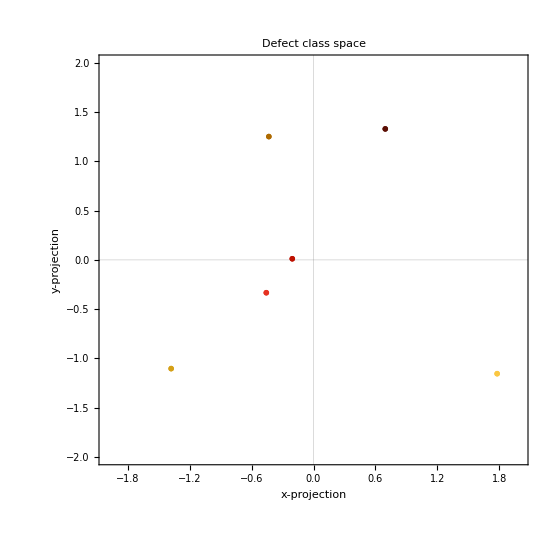

```mathematica
plotStyleC={AspectRatio->1,PlotRange->{{-2,2},{-2,2}},PlotTheme->"Scientific",Frame->True,PlotStyle->Directive[Black,Thickness[0.006]],FrameLabel->{Style["x-projection",18,Black],Style["y-projection",18,Black]},FrameStyle->Directive[18,Black,Thickness[0.004]]};
bigName[a_]:=Style[a,24,FontFamily->Times]
bigName@fullNames;
ListPlot[List/@xy,PlotMarkers->(bigName/@fullNames),Frame->True,PlotStyle->20,plotStyleC,ImageSize->550,PlotLabel->Style["Defect class space",20,Black]]
```

```mathematica
plotStyleD={AxesStyle->Directive[Black, 22],AspectRatio->1,PlotRange->{{-2,2},{-2,2}},PlotTheme->"Scientific",Boxed->True,BoxStyle->Thickness[0.009],PlotStyle->Directive[Black,Thickness[0.06]],AxesLabel->{Style["x-projection",18,Black],Style["y-projection",18,Black],Style["z-projection",18,Black]}};
ListPointPlot3D[Table[{xyz[[i]]},{i,1,6}],AspectRatio->1,ImageSize->550,PlotStyle->PointSize[0.1],PlotLegends->fullNames,plotStyleD]
```

-Graphics3D-

```mathematica
feet1=Table[FeatureExtract[Table[valData[[types]][[temps]][[1]],{types,1,6}]],{temps,1,5}];
feet1//Dimensions
```

{5,6,5}

```mathematica
xy1=Table[DimensionReduce[feet1[[i]],2],{i,1,5}]
xyz1=Table[DimensionReduce[feet1[[i]],3],{i,1,5}]
```

{{{-0.205802,0.0113773},{-0.457686,-0.33344},{0.696031,1.32973},{-0.433012,1.25172},{-1.38028,-1.10394},{1.78074,-1.15544}},{{-0.213526,-0.278082},{-0.469224,0.202828},{1.21243,0.514762},{-0.450795,-1.98217},{-1.46386,1.27014},{1.38497,0.272523}},{{0.184451,0.0542975},{0.399066,-0.346771},{-1.05997,1.31077},{0.841474,1.25482},{1.21543,-1.11975},{-1.58045,-1.15337}},{{-0.246381,0.267637},{-0.400598,0.0704661},{0.880946,1.76842},{-0.458332,0.129652},{-1.43176,-0.744553},{1.65612,-1.49162}},{{-0.362875,-0.275351},{-0.487612,0.00962805},{0.387212,-1.8743},{-0.410826,-0.044193},{-1.13295,1.2011},{2.00705,0.983112}}}

{{{-0.205802,0.0113773,-0.522957},{-0.457686,-0.33344,-0.0346724},{0.696031,1.32973,1.65525},{-0.433012,1.25172,-1.46085},{-1.38028,-1.10394,0.808279},{1.78074,-1.15544,-0.445049}},{{-0.213526,-0.278082,1.05548},{-0.469224,0.202828,1.17192},{1.21243,0.514762,-1.35876},{-0.450795,-1.98217,-0.780538},{-1.46386,1.27014,-0.769732},{1.38497,0.272523,0.68162}},{{0.184451,0.0542975,-0.662572},{0.399066,-0.346771,-0.506945},{-1.05997,1.31077,1.43504},{0.841474,1.25482,-0.985348},{1.21543,-1.11975,1.36358},{-1.58045,-1.15337,-0.643752}},{{-0.246381,0.267637,0.626098},{-0.400598,0.0704661,0.214681},{0.880946,1.76842,-0.929933},{-0.458332,0.129652,1.63592},{-1.43176,-0.744553,-1.41551},{1.65612,-1.49162,-0.131264}},{{-0.362875,-0.275351,0.604429},{-0.487612,0.00962805,0.135369},{0.387212,-1.8743,-1.0164},{-0.410826,-0.044193,1.67612},{-1.13295,1.2011,-1.33007},{2.00705,0.983112,-0.069458}}}

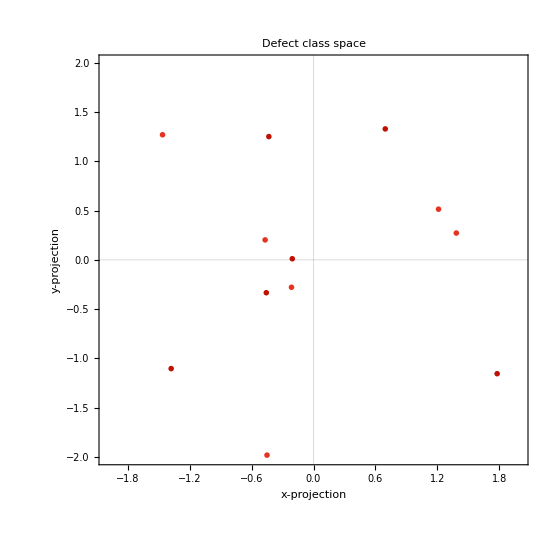

```mathematica
ListPlot[xy1[[1;;2]],PlotMarkers->(bigName/@fullNames),Frame->True,PlotStyle->20,plotStyleC,ImageSize->550,PlotLabel->Style["Defect class space",20,Black]]
```

```mathematica
Show@Table[ListPointPlot3D[Table[{xyz1[[temp]][[i]]},{i,1,6}],AspectRatio->1,ImageSize->550,PlotStyle->PointSize[0.1],PlotLegends->fullNames,plotStyleD],{temp,1,5}]
```

-Graphics3D-

## Import Final Test Data

```mathematica
(*Bound*)
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_129.4850/normal/full_version"];
filesTestVal129={"m.pdf.129.4850.760.B2-01_129.B3-130_154.txt","m.pdf.129.4850.1900.B2-01_108.B3-109_179.txt","m.pdf.129.4850.2500.B2-01_45.B3-46-128.txt",
"m.pdf.129.4850.3200.B2-01_30.B3-30-137.txt"};
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_142.4850/normal/full_version"];
filesTestVal142={"m.pdf.142.4850.1900.B3-01_111.B4-112_156.B3-157_199.txt","m.pdf.142.4850.2500.B3-01_109.B4-110_124.B3-125_140.B2-141_142.B3-143_146.B2-147_157.B3-158_176.txt",
"m.pdf.142.4850.3200.B3-01_60.B2-61_64.B3-65_123.B4-124_133.B3-134_183.txt","m.pdf.142.4850.3805.B3-01_20.B2-21_114.B3-115_143.txt"};

(*Unbound*)
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_70.4850/normal/full_version"];
filesTestVal70={"m.pdf.70.4850.3200.U2-01_169.U3-170_185.txt","m.pdf.70.4850.3805.U2-01_121.U3-122_131.U4-132_143.U3-144_172.txt"};

SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_174.4850/normal/full_version"];
filesTestVal174={"m.pdf.174.4850.3200.U3-01_81.U2-82_92.U3-93_166.U2-167_170.U3-171_185.txt","m.pdf.174.4850.3805.U3-01_158.U4-159_181.txt"};

SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_1126.4850/normal/full_version"];
filesTestVal1126={"m.pdf.1126.4850.760.U4-01_176.U3-177-187.txt","m.pdf.1126.4850.1900.U4-01_69.U3-70_164.txt","m.pdf.1126.4850.2500.U4-01_67.U3-68_157.txt","m.pdf.1126.4850.3200.U4-01_54.U3-55_153.txt"};

filesDefectTypesVal={filesTestVal129,filesTestVal142,filesTestVal70,filesTestVal174,filesTestVal1126};
dirList={"/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_129.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_142.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_70.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_174.4850/normal/full_version","/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/pdf_OUT_1126.4850/normal/full_version"};
```

```mathematica
pdfDataProTestVal=Table[Table[SetDirectory[dirList[[type]]];ReadList[filesDefectTypesVal[[type]][[temp]],{Number,Number,Number,Number,Number}],{temp,1,Length@filesDefectTypesVal[[type]]}],{type,1,5}];
```

```mathematica
proSum={#[[1]],0.5*(#[[3]]+#[[4]])}&;
proSum2={#[[1]],(#[[4]])}&;
CCdataSet=Table[Table[proSum2/@pdfDataProTestVal[[1]][[temp]],{temp,1,Length@filesDefectTypesVal[[type]]}],{type,1,5}]
```

{{1},3,{1}}
 |  |  |  |

```mathematica
filesDefectTypesVal[[1]]
```

{m.pdf.129.4850.760.B2-01_129.B3-130_154.txt,m.pdf.129.4850.1900.B2-01_108.B3-109_179.txt,m.pdf.129.4850.2500.B2-01_45.B3-46-128.txt,m.pdf.129.4850.3200.B2-01_30.B3-30-137.txt}

```mathematica
tList129={"760K","1900K","2500K","3200K"};
GraphicsGrid[{Table[ListLinePlot[Table[proSum2/@Partition[pdfDataProTestVal[[1]][[temp]],81][[timeStep]]/.{a_,b_}:>{a,15*b+timeStep},{timeStep,1,Length@Partition[pdfDataProTestVal[[1]][[temp]],81]}][[]],plotStyleA,AspectRatio->2,PlotLabel->Style[filesTestVal129[[temp]],14,Black]],{temp,1,filesTestVal129[[;;]]//Length}]},ImageSize->1500,Spacings->2]
```

-Graphics-

```mathematica
(*NOTE!!! 142 4850 3200, doesn't actually look like there is any B3*)
```

```mathematica
With[{type=2},GraphicsGrid[{Table[ListLinePlot[Table[proSum2/@Partition[pdfDataProTestVal[[type]][[temp]],81][[timeStep]]/.{a_,b_}:>{a,15*b+timeStep},{timeStep,1,Length@Partition[pdfDataProTestVal[[type]][[temp]],81]}][[]],plotStyleA,AspectRatio->2,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black]],{temp,1,filesDefectTypesVal[[type]][[;;]]//Length}]},ImageSize->1700,Spacings->2]]
```

-Graphics-

```mathematica
With[{type=3},GraphicsGrid[{Table[ListLinePlot[Table[proSum2/@Partition[pdfDataProTestVal[[type]][[temp]],81][[timeStep]]/.{a_,b_}:>{a,15*b+timeStep},{timeStep,1,Length@Partition[pdfDataProTestVal[[type]][[temp]],81]}][[]],plotStyleA,AspectRatio->2,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black]],{temp,1,filesDefectTypesVal[[type]][[;;]]//Length}]},ImageSize->1000,Spacings->2]]
```

-Graphics-

```mathematica
(*Note!!!! This looks just like U3*)
With[{type=4},GraphicsGrid[{Table[ListLinePlot[Table[proSum2/@Partition[pdfDataProTestVal[[type]][[temp]],81][[timeStep]]/.{a_,b_}:>{a,15*b+timeStep},{timeStep,1,Length@Partition[pdfDataProTestVal[[type]][[temp]],81]}][[]],plotStyleA,AspectRatio->2,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black]],{temp,1,filesDefectTypesVal[[type]][[;;]]//Length}]},ImageSize->1000,Spacings->2]]
```

-Graphics-

```mathematica
With[{type=5},GraphicsGrid[{Table[ListLinePlot[Table[proSum2/@Partition[pdfDataProTestVal[[type]][[temp]],81][[timeStep]]/.{a_,b_}:>{a,15*b+timeStep},{timeStep,1,Length@Partition[pdfDataProTestVal[[type]][[temp]],81]}][[]],plotStyleA,AspectRatio->2,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black]],{temp,1,filesDefectTypesVal[[type]][[;;]]//Length}]},ImageSize->1500,Spacings->2]]
```

-Graphics-

```mathematica
filesDefectTypesVal
```

{{m.pdf.129.4850.760.B2-01_129.B3-130_154.txt,m.pdf.129.4850.1900.B2-01_108.B3-109_179.txt,m.pdf.129.4850.2500.B2-01_45.B3-46-128.txt,m.pdf.129.4850.3200.B2-01_30.B3-30-137.txt},{m.pdf.142.4850.1900.B3-01_111.B4-112_156.B3-157_199.txt,m.pdf.142.4850.2500.B3-01_109.B4-110_124.B3-125_140.B2-141_142.B3-143_146.B2-147_157.B3-158_176.txt,m.pdf.142.4850.3200.B3-01_60.B2-61_64.B3-65_123.B4-124_133.B3-134_183.txt,m.pdf.142.4850.3805.B3-01_20.B2-21_114.B3-115_143.txt},{m.pdf.70.4850.3200.U2-01_169.U3-170_185.txt,m.pdf.70.4850.3805.U2-01_121.U3-122_131.U4-132_143.U3-144_172.txt},{m.pdf.174.4850.3200.U3-01_81.U2-82_92.U3-93_166.U2-167_170.U3-171_185.txt,m.pdf.174.4850.3805.U3-01_158.U4-159_181.txt},{m.pdf.1126.4850.760.U4-01_176.U3-177-187.txt,m.pdf.1126.4850.1900.U4-01_69.U3-70_164.txt,m.pdf.1126.4850.2500.U4-01_67.U3-68_157.txt,m.pdf.1126.4850.3200.U4-01_54.U3-55_153.txt}}

```mathematica
testingValSet=Table[Table[Table[proSum/@Partition[pdfDataProTestVal[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTestVal[[type]][[temp]],81]}],{temp,1,filesDefectTypesVal[[type]]//Length}],{type,1,filesDefectTypesVal//Length}];
```

```mathematica
modelResults=Table[Table[Table[cSVM[testingValSet[[type]][[temp]][[timeStep]]],{timeStep,1,Length@testingValSet[[type]][[temp]]}],{temp,1,Length@testingValSet[[type]]}],{type,1,Length@testingValSet}];
```

```mathematica
rule=Table[fullNames[[i]]->i,{i,1,Length@fullNames}]
```

{Bound-dimer→1,Bound-trimer→2,Unbound-dimer→3,Unbound-trimer→4,Unbound-tetramer→5,Perfect→6}

```mathematica
tickS=Table[{i,Style[fullNames[[i]],18,Black]},{i,1,Length@fullNames}];
```

```mathematica
With[{temp=2,type=1},ListLinePlot[modelResults[[type]][[temp]]/.rule,PlotRange->All,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black],PlotStyle->Black,FrameStyle->Directive[18,Thickness[0.006],Black],FrameTicks->{{tickS,None},Automatic},PlotRange->{Automatic,{0,6}},Frame->True]]
```

-Graphics-

```mathematica
With[{temp=1,type=2},ListLinePlot[modelResults[[type]][[temp]]/.rule,PlotRange->All,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black],PlotStyle->Black,FrameStyle->Directive[18,Thickness[0.006],Black],FrameTicks->{{tickS,None},Automatic},PlotRange->{Automatic,{0,6}},Frame->True]]
```

-Graphics-

```mathematica
With[{temp=1,type=3},ListLinePlot[modelResults[[type]][[temp]]/.rule,PlotRange->All,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black],PlotStyle->Black,FrameStyle->Directive[18,Thickness[0.006],Black],FrameTicks->{{tickS,None},Automatic},PlotRange->{Automatic,{0,6}},Frame->True]]
```

-Graphics-

```mathematica
With[{temp=1,type=4},ListLinePlot[modelResults[[type]][[temp]]/.rule,PlotRange->All,PlotLabel->Style[filesDefectTypesVal[[type]][[temp]],12,Black],PlotStyle->Black,FrameStyle->Directive[18,Thickness[0.006],Black],FrameTicks->{{tickS,None},Automatic},PlotRange->{Automatic,{0,6}},Frame->True]]
```

-Graphics-

```mathematica
countNum=Table[Count[modelResults[[1]][[1]],fullNames[[type]]],{type,1,6}]
```

{129,25,0,0,0,0}

```mathematica
Table[Table[i+j-1,{i,1,countNum[[j]]}],{j,1,2}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}}

```mathematica
Table[Table[type,{}],{type,1,6}]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{},{},{},{}}

### C-C: Compute mean pdfs and look at width T dependence, compare to Einstein width, etc

```mathematica
ListLinePlot[Table[Table[Mean@Table[proSum2/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,6}],{type,6,6}][[1]],PlotRange->All,PlotLegends->temperatures,PlotStyle->Thickness[0.006]]
```

-Graphics-

```mathematica
dataAllT=Table[Table[Mean@Table[proSum2/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{type,6,6}][[1]],{temp,1,6}];
```

```mathematica
widths=Table[With[{data=dataAllT[[i]]},
f2[x_]:=If[4>x>3,Interpolation[data][x],0];
f3[x_]:=If[5>x>4,Interpolation[data][x],0];
data2=Table[{x,f2[x]},{x,3,4,0.001}];
data3=Table[{x,f3[x]},{x,4,5,0.001}];
nonlinFitA=NonlinearModelFit[data2,c*PDF[NormalDistribution[a,b],x],{a,b,c},x];
nonlinFitB=NonlinearModelFit[data3,h*PDF[NormalDistribution[f,g],x],{f,g,h},x];
nonlinFit[x_]:=nonlinFitA[x]+nonlinFitB[x];
Plot[nonlinFit[x],{x,0,5},PlotRange->All];
nonlinFitA[[1]][[2]][[2]]
nonlinFitB[[1]][[2]][[2]]],{i,1,6}]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{(b→0.0779693) (g→0.0759679),(b→0.115517) (g→0.103846),(b→0.182626) (g→0.159983),(b→0.208016) (g→0.184475),(b→0.233264) (g→0.214187),(b→0.25152) (g→0.254323)}

{0.0779693,0.115517,0.182626,0.208016,0.233264,0.25152}

{0.0759679,0.103846,0.159983,0.184475,0.214187,0.254323}

{1.02634,1.11239,1.14153,1.12761,1.08906,0.988977}

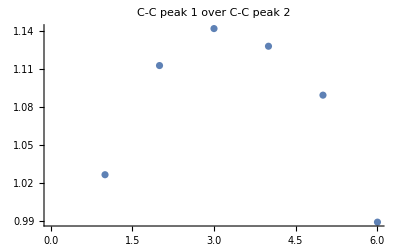

{1.,1.48157,2.34228,2.66792,2.99174,3.22588}

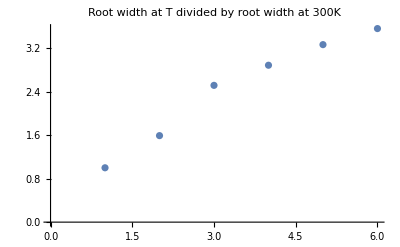

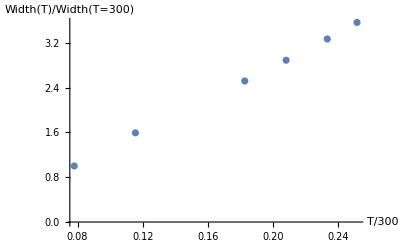

```mathematica
(*b is lower band, g is upper*)
temps={300,760,1900,2500,3200,3805};
bWidths=Table[b/.widths[[i]][[1]],{i,1,6}]
gWidhts=Table[g/.widths[[i]][[2]],{i,1,6}]
bWidths/gWidhts
ListPlot[(bWidths/gWidhts),PlotLabel->"C-C peak 1 over C-C peak 2"]

scaleFactors300=bWidths/bWidths[[1]]
ListPlot[Sqrt[temps/temps[[1]]]//N,PlotLabel->"Root width at T divided by root width at 300K"]
ListPlot[Table[{bWidths[[i]],(Sqrt[temps/temps[[1]]])[[i]]},{i,1,6}],AxesLabel->{"T/300","Width(T)/Width(T=300)"}]
```

```mathematica
proSum2={#[[1]],#[[4]]}&;
proSum3={#[[1]],#[[2]]}&;
```

#### Zr-Zr: PDF means

```mathematica
ListLinePlot[Table[Table[Mean@Table[proSum3/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{temp,1,6}],{type,6,6}][[1]],PlotRange->All,PlotLegends->temperatures,PlotStyle->Thickness[0.006]]
```

-Graphics-

```mathematica
dataAllTzrzr=Table[Table[Mean@Table[proSum3/@Partition[pdfDataProTest[[type]][[temp]],81][[timeStep]],{timeStep,1,Length@Partition[pdfDataProTest[[type]][[temp]],81]}],{type,6,6}][[1]],{temp,1,6}];
```

```mathematica
widthsZrZr=Table[With[{data=dataAllTzrzr[[i]]},
f2[x_]:=If[4>x>3,Interpolation[data][x],0];
f3[x_]:=If[5>x>4,Interpolation[data][x],0];
data2=Table[{x,f2[x]},{x,3,4,0.001}];
data3=Table[{x,f3[x]},{x,4,5,0.001}];
Clear[a,b,c,d,e,f,g,h];
Clear[nonlinFitA,nonlinFitB];
nonlinFitA=NonlinearModelFit[data2,c*PDF[NormalDistribution[a,b],x],{a,b,c},x];
nonlinFitB=NonlinearModelFit[data3,h*PDF[NormalDistribution[f,g],x],{f,g,h},x];
nonlinFit[x_]:=nonlinFitA[x]+nonlinFitB[x];
Plot[nonlinFit[x],{x,0,5},PlotRange->All];
nonlinFitA[[1]][[2]][[2]]
nonlinFitB[[1]][[2]][[2]]],{i,1,6}]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{(b→0.0693585) (g→0.0755292),(b→0.100893) (g→0.10729),(b→0.15904) (g→0.157668),(b→0.179738) (g→0.186407),(b→0.202771) (g→0.208632),(b→0.221567) (g→0.242302)}

{0.0693585,0.100893,0.15904,0.179738,0.202771,0.221567}

{0.0755292,0.10729,0.157668,0.186407,0.208632,0.242302}

{0.9183,0.940369,1.0087,0.964224,0.971909,0.914427}

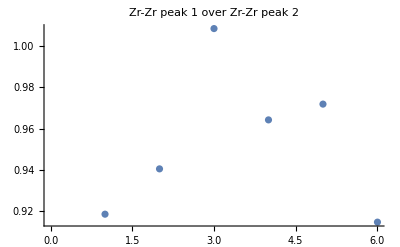

{1.,1.45465,2.29301,2.59144,2.92352,3.19452}

-Graphics-

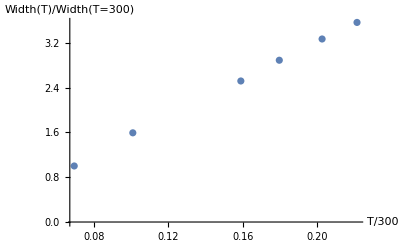

```mathematica
temps={300,760,1900,2500,3200,3805};
bWidths=Table[b/.widthsZrZr[[i]][[1]],{i,1,6}]
gWidhts=Table[g/.widthsZrZr[[i]][[2]],{i,1,6}]
bWidths/gWidhts
ListPlot[(bWidths/gWidhts),PlotLabel->"Zr-Zr peak 1 over Zr-Zr peak 2"]

scaleFactors300=bWidths/bWidths[[1]]
ListPlot[Sqrt[temps/temps[[1]]]//N,PlotLabel->"Root width at T divided by root width at 300K"]
ListPlot[Table[{bWidths[[i]],(Sqrt[temps/temps[[1]]])[[i]]},{i,1,6}],AxesLabel->{"T/300","Width(T)/Width(T=300)"}]
```

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[15,scaleFactors300[[i]]],x],{i,1,6}],{x,5,25},PlotRange->All,PlotLegends->temperatures,PlotStyle->Thickness[0.006],Frame->True]
```

-Graphics-

```mathematica
RandomReal[1]
```

0.802294

```mathematica
NormalDistribution[0.5,1]
```

NormalDistribution[0.5,1]

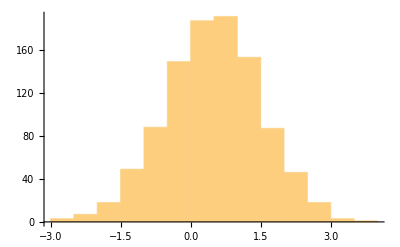

```mathematica
Histogram@RandomVariate[NormalDistribution[0.5,1],1000]
```

```mathematica
normalData=Table[{x,PDF[NormalDistribution[5,1],x]}/.x->RandomReal[10],100];
```

```mathematica
RandomVariate[NormalDistribution[5,1],1]
```

{5.37446}

```mathematica
normalFilter[{a_,b_}]:={a,(PDF[NormalDistribution[5,1],a]+b)/2}
normalFilter2[{a_,b_}]:={a,(RandomVariate[NormalDistribution[5,1.4],1]+b)/2}
Show[{ListPlot[normalFilter2/@normalData,PlotStyle->Red],ListPlot[normalData]},PlotRange->All]
```

-Graphics-

```mathematica
normalData[[1]]
```

{0.537901,0.0000189425}

```mathematica
normalFilter[normalData[[1]]]
```

{0.537901,3.58819×10^-10}

```mathematica
ListPlot@normalData
```

-Graphics-

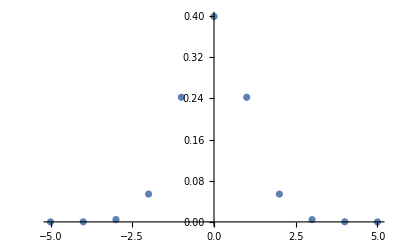

```mathematica
ListPlot@Table[{x,PDF[NormalDistribution[0,1],x]},{x,-5,5}]//N
```

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5}]
```

-Graphics-

```mathematica
fun=Assuming[μ∈Reals&&σ>0&&y∈Reals,FullSimplify[Integrate[PDF[NormalDistribution[μ,σ],x] DiracDelta[1.5*x-y],{x,-∞,∞},Assumptions->μ∈Reals&&σ>0&&y∈Reals]]]
```

(0.265962 ⅇ^((-0.222222 y^2+0.666667 y μ-0.5 μ^2)/σ^2))/σ

```mathematica
Plot[{fun/.{μ->0,σ->1},PDF[NormalDistribution[μ,σ],y]/.{μ->0,σ->1} },{y,-5,5}]
```

-Graphics-

```mathematica
Conv
```

```mathematica
ListLinePlot@Table[Mean@testingValSet[[1]][[i]][[1;;100]],{i,1,4}]
```

-Graphics-

```mathematica
ListLinePlot@Table[Mean@testingValSet[[1]][[i]][[1;;100]],{i,1,4}]
```

```mathematica
(*http://reference.wolfram.com/language/ref/ListDeconvolve.html*)
h=Transpose[testingValSet[[1]][[1]][[1]]][[2]]
g=Transpose[testingValSet[[1]][[1]][[100]]][[2]]
tmp=Map[ListDeconvolve[h,g,Method->"RichardsonLucy",MaxIterations->#,Padding->"Periodic"]&,Range[1,30]];
```

{0.,0.,0.,0.,0.,0.,0.,0.0273,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0215,0.0154,0.0049,0.0423,0.08555,0.51375,0.116,0.00795,0.02675,0.,0.0071,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.03195,0.09305,0.5249,0.0794,0.03045,0.0079,0.0115,0.00375,0.,0.00355,0.00345,0.,0.0098,0.0032,0.0062,0.01365,0.037,0.1473,0.10715,0.03165,0.01615,0.00655,0.,0.00625,0.00245,0.0024,0.00235,0.,0.0045,0.011,0.0842,0.08245,0.0124,0.0061,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.0254,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00565,0.0215,0.0257,0.06875,0.13635,0.1351,0.1554,0.12015,0.0756,0.05735,0.02575,0.0071,0.0034,0.0033,0.,0.00305,0.,0.,0.,0.,0.0052,0.005,0.03885,0.07535,0.06395,0.1551,0.1097,0.10445,0.1218,0.06315,0.03455,0.,0.,0.0053,0.01205,0.01005,0.00815,0.00795,0.0264,0.0485,0.05175,0.05055,0.0578,0.0482,0.04035,0.02105,0.0077,0.0063,0.00125,0.0048,0.00705,0.01265,0.01125,0.03195,0.0324,0.0444,0.03005,0.01115,0.}

```mathematica
ListLinePlot[Transpose[tmp],PlotStyle->Black,PlotRange->All,AspectRatio->2/3,Epilog->{PointSize[Medium],{Blue,Point[Thread[{1,tmp[[1]]}]]},{Red,Point[Thread[{30,f}]]}}]
```

-Graphics-

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/Frenkels_classifier_dataSet/pdf_ALL_results/"];
filesTest70={"pdf_OUT_70.4850/normal/m.pdf.70.4850.760.U2-01_223.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.1900.U2-01_169.txt",
"pdf_OUT_70.4850/normal/m.pdf.70.4850.2500.U2-01_171.txt","pdf_OUT_70.4850/normal/m.pdf.70.4850.3200.U2-01_169.txt",
"pdf_OUT_70.4850/normal/m.pdf.70.4850.3805.U2-01_121.txt"};
pdfDataTest=Table[ReadList[filesTest70[[i]],{Number,Number,Number,Number,Number}],{i,1,Length@filesTest70}];


zrzrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[2]]},{i,1,5}];
czrTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[3]]},{i,1,5}];
ccTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[4]]},{i,1,5}];
totTest=Table[Transpose@{Transpose[pdfDataTest[[i]]][[1]],Transpose[pdfDataTest[[i]]][[5]]},{i,1,5}];
```

```mathematica
Table[Partition[pdfDataTest[[i]],81]//Length,{i,1,Length@pdfDataTest}]
```

{223,169,196,169,121}

#### PDF plot, animation, and export;

```mathematica
ListLinePlot[Partition[ccTest[[5]],81][[]],plotStyle]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[ccTest[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,120}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[zrzrTest[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,120}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListLinePlot[Table[Partition[czrTest[[j]],81][[i]]/.{a_,b_}:>{a,b+i/10},{i,1,120}],plotStyleA,AspectRatio->3],{j,1,5}]},ImageSize->1300,Spacings->2]
```

-Graphics-

```mathematica
(*ccTestAnimation=Table[With[{name=ccTest},ListAnimate[Table[ListLinePlot[Partition[name[[j]],81][[i]],plotStyle,PlotLabel->Style[volumes[[j]],18,Black]],{i,1,Partition[name[[j]],81]//Length}],25]],{j,1,2}]*)
```

```mathematica
(*SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Frenkel_classifier/Frenkels_classifier_training_structures/animations"];
framesTestingCC=Table[With[{name=ccTest},Table[ListLinePlot[Partition[name[[j]],81][[i]],Frame->True,plotStyle,PlotLabel->Style["3000 K MD",18,Black]],{i,1,Partition[name[[j]],81]//Length}]],{j,1,1}];
framesTestingCCJoined=Join[framesTestingCC[[1]],framesTestingCC[[1]]];
Export["framesTestingCC.gif",framesTestingCCJoined,"AnimationRepetitions"->1,"ControlAppearance"->None]*)
```